```mathematica
Lecture 15: Game Theory
```

Game Theory is the mathematical analysis of conflict and cooperation.

## Matrix Games

### Exercise Subsection

A matrix game on a matrix A has two players: a row player and a column player.  The row player secretly selects a row r, the column player secretly selects a column c.  When choices are revealed, the row player earns A[[r,c]] from the column player.  Therefore the row player wants to maximize A[[r,c]] and the column player wants to minimize A[[r,c]].

For example, the matrix in the next cell models “rock, paper, scissors” with the winner earning $1 from the loser.

```mathematica
A={{0,-1,1},{1,0,-1},{-1,1,0}};
TableForm[A,TableHeadings->{{"Rock","Paper","Scissors"},{"Rock","Paper","Scissors"}}]
```

| Rock | Paper | Scissors
Rock | 0 | -1 | 1
Paper | 1 | 0 | -1
Scissors | -1 | 1 | 0

An optimal strategy for the row (or column) player is a probability vector that gives the probability that a rational and intelligent player should play each row.  Finding optimal row and column strategies can be found using the code in the next cell.

```mathematica
RowStrategy[P_]:=Module[{d=Dimensions@P,L},(L=LinearProgramming[Table[1,d[[1]]],Transpose@P+1-Min@P,Table[1,d[[2]]]])/Total@L]
ColStrategy[P_]:=RowStrategy@Transpose[-P]
```

For example, for the “rock, paper, scissors” matrix A defined above, the next cell gives the (somewhat obvious) optimal strategies for the row and column player:

```mathematica
RowStrategy@A
ColStrategy@A
```

{1/3,1/3,1/3}

{1/3,1/3,1/3}

### Exercise Subsection

There are occasionally penalty kicks in soccer. Each penalty kick involves only a kicker and a goalie.  1417 actual penalty kicks in professional soccer matches were analyzed to arrive at this matrix game, where the kicker is the row player, the goalie is the column player, and the entries give the probability of a goal.

```mathematica
soccer={{.58,.95},{.93,.7}};
TableForm[soccer,TableHeadings->{{"Kick right","Kick left"},{"Anticipate right","Anticipate left"}}]
```

| Anticipate right | Anticipate left
Kick right | 0.58 | 0.95
Kick left | 0.93 | 0.7

Give the optimal strategies for the kicker and the goalie.

```mathematica
RowStrategy@soccer
```

{0.383333,0.616667}

```mathematica
ColStrategy@soccer
```

{0.416667,0.583333}

### Exercise Subsection

Rose secretly writes down a number between 1 and n. Colin repeatedly guesses Rose's number until guessing correctly.  After an incorrect guess of k, Rose tells Colin if his guess is higher or lower than k . At the end of the game, Colin pays Rose the number of guesses it took to ﬁnd Rose's secret number.

The strategies for Rose are the numbers 1 through n.  The strategies for Colin are the permutations of 1,...,n where the permutation gives the sequence of guesses (with guesses that are known to be wrong skipped). 

Find the optimal row (Rose) and column (Colin) strategies in the case n = 6 by doing the following:
1. Define a function Payoff[r_,col_] with input an integer r between 1 and 6 and a permutation col of 1,...,6 and output the number of guesses taken to find r using the strategy col.  I was able to do this efficiently by recursively defining Payoff.
2. Create the matrix with entries Payoff[r_,col_] where r, col range over all possible strategies.
3. Apply RowStrategy and ColStrategy (as defined in Lecture15) to solve the matrix game.

It is an open problem to find an optimal column strategy for this game for large n.

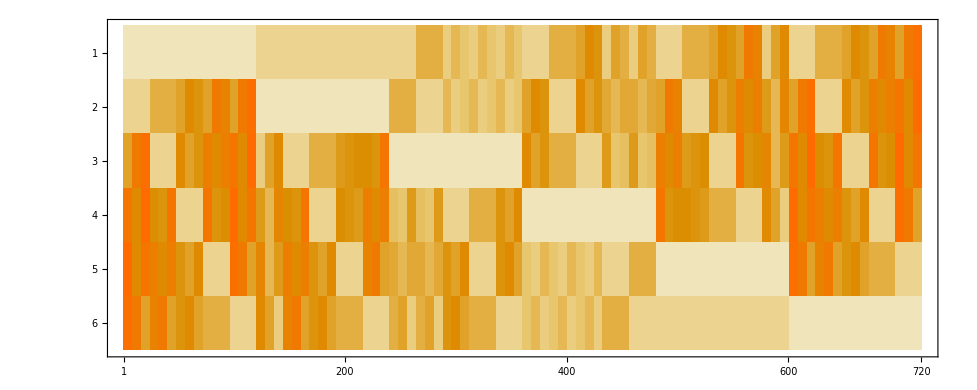

```mathematica
Payoff[k_,col_]:=1+Module[{g=col[[1]]},Which[g==k,0,g<k,Payoff[k,Cases[col,a_/;a>g]],g>k,Payoff[k,Cases[col,a_/;a<g]]]]
A=Table[Payoff[k, col], {k, Range@6}, {col, Permutations@Range@6}] ;
A//MatrixPlot
```

```mathematica
RowStrategy@A//N
```

{0.25,0.15,0.1,0.1,0.15,0.25}

```mathematica
(Permutations@Range@6)[[Flatten@Position[ColStrategy@A,a_/;a>0]]]
```

{{2,1,5,3,4,6},{3,1,2,5,4,6},{3,1,2,6,5,4},{4,1,2,3,6,5},{4,2,1,3,6,5},{5,2,1,4,3,6}}

```mathematica
Cases[ColStrategy@A,a_/;a>0]
```

{1/10,3/10,1/10,1/10,3/10,1/10}

```mathematica
20!
```

2432902008176640000

### Exercise Subsection

A random integer r between 1 and 100 is selected.  Two players both try to guess r, and the player that is closest without going over is the winner (like the Price is Right game show). 

a. Write a function named Payoff[i_,j_,r_] that has input the guess i for the first player, the guess j for the second player, the integer r between 1 and 100.  The output should be 1 if the first player wins, -1 if the second player wins, and 0 if there is a tie or neither player wins.

```mathematica
Payoff[i_,j_,r_]:=Which[i==j,0,r<Min[{i,j}],0,i<=r<j,1,i<j<=r,-1,j<=r<i,-1,j<i<=r,1]
```

b.  Once Payoff has been defined, then the expected payoff matrix A is defined below:

```mathematica
A=Table[N@Sum[Payoff[i,j,r]/100,{r,100}],{i,100},{j,100}];
```

Use RowStrategy@A to find an optimal strategy for the row player.  Then use ListPlot together with Accumulate on this strategy to estimate the probability that an optimal strategy will play an integer <=i for i between 0 and 75.  This plot should be close to the plot of the solution to the differential equation in the next cell, find and plot the solution on the same graph.

```mathematica
PriceIsRightDE={0==(2x−200)y'[x]+1+y[x],y[0]==0};
```

## Nonzero sum games

### Exercise Subsection

The prisoner’s dilemma is a two player game where each player can cooperate for mutual benefit or betray for individual reward.  The payoffs to each player are given in the table below, with the entries giving the payoff to the row and column player, respectively.

```mathematica
dilemma={{{1,1},{-1,2}},{{2,-1},{0,0}}};
TableForm[ToString/@#&/@dilemma,TableHeadings->{{"Row 1: Cooperate","Row 2: Betray"},{"Col 1: Cooperate","Col 2: Betray"}}]
```

| Col 1: Cooperate | Col 2: Betray
Row 1: Cooperate | {1, 1} | {-1, 2}
Row 2: Betray | {2, -1} | {0, 0}

This game will be played a large number of times in a row (on the order of 1000, say), and the history of play is recorded as a sequence of 1’s and 2’s.  The next cell defines 8 different strategies, each taking in a list H of the history of their opponent’s play and outputs either a 1 or a 2.

```mathematica
Pushover[H_]:=1
TotalJerk[H_]:=2
TitForTat[H_]:=If[H=={},1,H[[-1]]]
ICanForgive[H_]:=Which[H=={},1,H[[-1]]==2,RandomChoice[{.1,.9}->{1,2}],True,1]
WeightedRandom[H_]:=RandomChoice[{.6,.4}->{1,2}]
YouDidThisToMe[H_]:=If[H=={},1,RandomChoice@H]
DontMakeMeMad[H_]:=If[Count[H,2]>=10,2,1]
FalseFront[H_]:=If[Count[H,2]<=10,2,1]
FoolMeTwice[H_]:=Which[Length@H<2,1,H[[-2;;]]=={2,2},2,True,1]
HalfAndHalf[H_]:=If[EvenQ@Length@H,1,2]
DontMakeMeMadder[H_]:=If[Count[H,2]>=11,2,1]
AlmostMad[H_]:=If[Length@H<=4,2,1]
```

The code in the next cell defines a function Compete which outputs the total score when two strategies S1 and S2 compete n times.

```mathematica
Compete[S1_,S2_,n_]:=Module[{H1={},H2={},score={0,0}},
Do[Module[{p1=S1@H2,p2=S2@H1},
AppendTo[H1,p1];
AppendTo[H2,p2];
score+=dilemma[[p1,p2]]],n];
score]
Compete[TitForTat,WeightedRandom,1000]
```

{582,585}

From here we can run a tournament that pits each strategy against each other strategy:

```mathematica
StrategyList={Pushover,TotalJerk,TitForTat,ICanForgive,WeightedRandom,YouDidThisToMe,DontMakeMeMad,FalseFront,FoolMeTwice,HalfAndHalf,DontMakeMeMadder,AlmostMad};
scores=Flatten[Transpose@{#,Compete[First@#,Last@#,1000]}&/@Subsets[StrategyList,{2}],1];
SortBy[Table[{s,Total@Cases[scores,{s,a_}->a]},{s,StrategyList}],Last]//Reverse//TableForm
```

DontMakeMeMadder | 11127
DontMakeMeMad | 11099
YouDidThisToMe | 9122
TitForTat | 9068
ICanForgive | 8882
TotalJerk | 8444
FoolMeTwice | 8363
HalfAndHalf | 6884
WeightedRandom | 5751
Pushover | 5256
FalseFront | 5207
AlmostMad | 5113

Come up with a new strategy that is not on the current list, and then rerun the tournament with your strategy included to see how it fares.

## Learning from experience

### Exercise Subsection

Solutions to matrix games can be approximated by having the row and column players learning from the experience of playing many times over.  For example, consider the matrix game A below:

```mathematica
A={{-2,0,-3,3,-2},{3,-2,2,3,2},{3,2,3,-2,3}};
```

Implement this idea to approximate the optimal strategies for A, and then compare with the strategies found with RowStrategy and ColumnStrategy.

1. Initialize row and col to be the vectors of the appropriate length with each entry 1 (in the above example row has length 3 and col has length 5).  This will mean that every row and column is equally likely to be selected initially.
2. Let r be a position of maximum entry in the matrix multiplication A.col.  Update row by adding 1 to position r in row.
3. Let c be a position of minimum entry in the matrix multiplication row.A.  Update col by adding 1 to position c in col.
4. Repeat steps 3 through 4 many times.  The approximate optimal strategies are row/Total@row and col/Total@col.

### Exercise Subsection

You and Colonel Blotto both have 100 soldiers which are to be distributed to 10 battleﬁelds. Secretly and independently, each commander divides the 100 forces into 10 parts and sends each part to a battleﬁeld. Ten ﬁghts take place, and the larger army wins at each battleﬁeld (neither army wins if the forces are the same size). The ultimate winner is the player who won the most battles. 

For example, if you use the strategy {10,10,10,10,10,10,10,10,10,10} and Colonel Blotto uses the strategy {2,11,11,11,11,11,11,11,11,10}, then Colonel Blotto wins because he won 8 battles to your 1.

a. Write a function named Blotto that inputs two lists of length 10 that sum to 100 (and has a check on the input pattern to make sure that the strategies have this property) and outputs 1 if the first strategy defeats the second, 0 if the strategies tie, and -1 otherwise.

b. The file at https://anthonymendes.github.io/Blotto.m contains a list of 167 blotto strategies submitted by former game theory students.  Each strategy S1 in the list earns a total score by summing the value of Blotto when S1 competes against every other strategy in the list.  Sort the list from the best scoring to the worst scoring.

```mathematica
strategies=Import["https://anthonymendes.github.io/Blotto.m"];
```

```mathematica
strategies//Length
```

167

c. Find a strategy that would score higher than all other strategies if it were added to the list of 167 strategies and then the competition in part b was repeated.

```mathematica
Blotto[S1_List/;Length@S1==10&&Total@S1==100,S2_List/;Length@S2==10&&Total@S2==100]:=
Module[{wins=Count[S1-S2,_?Positive],loss=Count[S1-S2,_?Negative]},
Which[wins>loss,1,wins<loss,-1,True,0]]
```

```mathematica
Score[S1_]:=Total[Blotto[S1,#]&/@strategies]
{Score[#],#}&/@SortBy[strategies,Score]//Reverse
```

{{88,{5,6,20,8,19,2,8,21,7,4}},{82,{5,7,19,6,20,7,7,19,6,4}},{80,{5,7,19,6,20,6,7,19,7,4}},{71,{19,7,6,7,20,19,7,4,6,5}},{68,{5,8,2,19,4,19,17,5,18,3}},{67,{10,19,19,4,1,19,1,19,3,5}},{65,{5,5,18,5,5,17,18,17,5,5}},{62,{18,18,5,5,3,18,5,18,5,5}},{62,{5,5,17,5,5,18,5,18,18,4}},{61,{7,6,18,21,4,19,7,6,5,7}},{61,{7,4,18,6,6,19,19,17,1,3}},{60,{3,18,19,4,5,4,19,4,20,4}},{59,{5,20,5,22,23,5,5,5,5,5}},{58,{5,5,4,5,18,18,5,18,17,5}},{57,{4,6,19,16,18,17,8,2,7,3}},{56,{5,4,18,5,18,5,5,18,18,4}},{55,{19,5,5,18,5,19,4,5,17,3}},{54,{5,5,5,18,18,17,5,5,5,17}},{52,{18,18,18,18,5,4,6,4,4,5}},{51,{18,6,4,17,6,5,18,4,5,17}},{50,{6,6,18,0,6,17,18,17,6,6}},{50,{4,5,4,5,19,5,18,4,18,18}},{49,{18,18,5,5,18,5,5,4,18,4}},{48,{18,5,4,5,18,5,18,18,4,5}},{46,{4,18,18,3,1,17,17,17,3,2}},{44,{17,6,17,7,6,17,8,7,7,8}},{44,{3,18,18,2,3,18,2,3,18,15}},{43,{20,5,20,5,18,5,10,5,5,7}},{42,{2,18,17,7,19,8,7,2,17,3}},{42,{1,3,19,3,17,3,17,17,17,3}},{40,{18,2,2,18,18,2,2,18,18,2}},{39,{1,19,18,2,1,18,1,20,18,2}},{37,{3,17,17,3,3,17,17,3,17,3}},{37,{2,7,18,17,19,17,2,8,7,3}},{36,{22,7,7,7,7,7,7,22,7,7}},{36,{3,2,18,3,17,2,18,17,3,17}},{35,{17,3,3,17,3,17,17,17,3,3}},{33,{4,4,18,18,1,18,1,18,18,0}},{33,{2,18,2,18,2,18,2,18,2,18}},{33,{2,8,18,22,0,0,22,18,8,2}},{29,{18,2,18,2,18,2,18,2,18,2}},{29,{17,3,2,1,18,19,3,17,18,2}},{29,{3,17,3,17,3,17,3,17,3,17}},{29,{3,3,17,3,17,17,17,17,3,3}},{29,{2,18,1,3,19,17,3,2,17,18}},{29,{2,17,3,18,17,2,18,3,2,18}},{29,{1,1,1,19,19,19,19,19,1,1}},{28,{3,3,18,17,18,17,17,3,2,2}},{27,{19,1,19,1,19,1,19,1,19,1}},{27,{19,1,19,1,19,1,19,1,19,1}},{27,{19,1,19,1,19,1,19,1,19,1}},{27,{1,1,1,1,1,19,19,19,19,19}},{26,{2,2,2,2,0,21,18,18,17,18}},{25,{17,5,16,2,20,8,5,17,7,3}},{23,{19,3,3,3,19,19,5,7,3,19}},{23,{1,20,19,3,17,3,17,3,16,1}},{21,{19,5,18,3,17,15,16,2,1,4}},{21,{18,18,18,18,18,2,2,2,2,2}},{20,{20,2,2,2,2,2,20,18,17,15}},{18,{11,14,21,2,2,2,2,21,14,11}},{15,{19,5,18,3,17,15,16,3,1,3}},{15,{1,6,8,14,21,21,14,8,6,1}},{13,{16,17,0,17,0,0,17,0,17,16}},{13,{2,1,18,12,15,21,7,4,19,1}},{12,{4,14,15,6,17,3,16,8,5,12}},{11,{20,0,20,0,20,0,20,0,20,0}},{11,{4,4,16,16,4,4,16,16,16,4}},{11,{0,20,0,20,0,20,0,20,0,20}},{10,{0,0,0,20,20,20,20,20,0,0}},{9,{1,1,2,9,21,21,0,21,3,21}},{8,{0,0,0,0,0,20,20,20,20,20}},{7,{20,21,1,1,18,18,1,19,0,1}},{6,{1,20,1,1,20,20,1,20,15,1}},{5,{2,18,10,2,10,2,18,2,18,18}},{2,{15,13,1,17,1,2,13,1,18,19}},{2,{1,19,15,12,2,1,11,19,19,1}},{2,{0,0,0,1,17,16,17,16,17,16}},{1,{17,17,0,17,0,0,16,0,16,17}},{1,{8,9,13,16,4,4,16,13,9,8}},{1,{4,16,3,16,6,16,4,16,3,16}},{1,{0,18,17,0,17,18,5,5,20,0}},{-1,{5,5,5,4,3,15,15,16,17,15}},{-2,{0,16,17,0,17,17,16,0,0,17}},{-3,{18,2,2,22,6,26,2,2,18,2}},{-4,{23,4,18,17,3,4,3,10,2,16}},{-4,{7,7,12,12,12,12,12,12,7,7}},{-4,{0,0,0,0,16,16,17,17,17,17}},{-6,{0,18,0,19,0,20,0,21,0,22}},{-7,{17,16,17,17,16,17,0,0,0,0}},{-9,{16,4,17,2,16,3,16,11,12,3}},{-10,{0,0,17,17,16,16,17,17,0,0}},{-10,{0,0,17,17,16,16,17,17,0,0}},{-12,{6,14,7,13,14,6,5,15,8,12}},{-12,{0,0,10,20,20,20,20,10,0,0}},{-14,{17,17,17,17,17,15,0,0,0,0}},{-14,{1,1,1,1,16,16,16,16,16,16}},{-14,{1,1,1,1,16,16,16,16,16,16}},{-14,{1,1,1,1,16,16,16,16,16,16}},{-15,{0,19,0,18,0,10,16,0,17,20}},{-16,{8,10,8,10,12,11,10,11,10,10}},{-17,{2,2,16,16,16,16,14,14,2,2}},{-18,{16,15,3,17,1,10,13,7,14,4}},{-18,{5,15,5,15,5,15,5,15,5,15}},{-18,{5,15,5,15,5,15,5,15,5,15}},{-18,{5,15,5,15,5,15,5,15,5,15}},{-19,{11,10,5,8,14,7,10,13,14,8}},{-19,{1,1,16,16,16,16,16,16,1,1}},{-19,{1,1,16,16,16,16,16,16,1,1}},{-20,{18,0,16,16,0,17,17,0,0,16}},{-20,{12,12,11,11,11,10,10,9,9,5}},{-21,{7,13,13,7,13,7,7,13,7,13}},{-21,{5,12,11,9,16,9,13,9,11,5}},{-22,{11,11,11,11,11,9,10,10,9,7}},{-23,{16,16,16,1,16,1,16,16,1,1}},{-23,{16,1,16,16,16,1,16,1,16,1}},{-23,{7,15,4,4,4,15,5,15,16,15}},{-24,{18,0,0,16,16,17,0,16,17,0}},{-24,{16,1,1,16,16,16,16,1,16,1}},{-24,{3,15,17,15,10,5,3,10,5,17}},{-25,{9,11,9,11,9,11,9,11,9,11}},{-25,{1,17,11,8,12,18,11,11,9,2}},{-25,{0,21,2,21,11,21,1,21,2,0}},{-26,{16,1,16,1,16,1,16,1,16,16}},{-26,{16,1,16,1,16,1,16,1,16,16}},{-27,{8,11,10,9,12,13,9,9,11,8}},{-28,{16,16,16,16,16,16,1,1,1,1}},{-28,{16,16,16,16,16,16,1,1,1,1}},{-28,{10,10,10,10,10,10,10,10,10,10}},{-31,{10,5,17,5,15,10,1,5,15,17}},{-32,{16,16,16,1,1,1,1,16,16,16}},{-32,{16,16,4,0,0,0,16,16,16,16}},{-33,{2,15,1,15,0,15,15,9,15,13}},{-33,{0,2,16,16,16,16,16,16,2,0}},{-33,{0,0,16,18,16,0,16,18,0,16}},{-34,{4,14,4,14,4,14,4,14,14,14}},{-34,{1,17,5,13,9,11,7,15,3,19}},{-35,{16,6,16,11,1,11,6,11,11,11}},{-38,{15,2,16,2,16,2,15,2,15,15}},{-38,{0,0,0,0,16,16,16,16,16,20}},{-38,{0,0,0,0,16,16,16,16,16,20}},{-40,{22,10,7,1,13,10,21,8,8,0}},{-41,{11,11,11,11,10,2,11,11,11,11}},{-41,{3,14,5,14,4,15,14,14,15,2}},{-41,{0,0,18,14,16,15,20,0,0,17}},{-42,{16,15,16,14,15,16,2,2,2,2}},{-42,{11,1,11,11,11,11,11,11,11,11}},{-44,{3,3,16,15,15,0,15,15,15,3}},{-45,{12,12,0,13,0,12,13,12,13,13}},{-46,{20,15,0,17,14,0,13,12,9,0}},{-47,{17,1,14,6,15,1,13,15,16,2}},{-49,{14,13,16,11,15,9,8,7,2,5}},{-54,{6,13,13,14,10,14,8,5,16,1}},{-54,{3,3,12,12,12,12,11,12,12,11}},{-55,{19,27,0,1,0,7,0,11,18,17}},{-57,{12,12,12,12,12,10,10,10,10,0}},{-58,{21,15,15,15,15,15,1,1,1,1}},{-59,{12,12,12,2,12,12,2,12,12,12}},{-62,{14,14,0,14,14,0,15,0,15,14}},{-62,{1,15,13,1,15,12,15,15,12,1}},{-65,{13,14,14,14,15,1,1,11,5,12}},{-67,{16,2,15,5,15,15,4,13,13,2}},{-69,{16,16,12,13,12,8,10,10,3,0}},{-72,{18,17,16,13,13,12,11,0,0,0}},{-78,{15,15,15,15,15,15,10,0,0,0}},{-82,{14,14,14,1,13,14,1,1,14,14}},{-85,{0,11,12,13,14,14,13,12,11,0}},{-90,{30,20,20,20,10,0,0,0,0,0}}}

```mathematica
Score/@({5,7,20,8,19,2,8,20,6,5}+#&/@Permutations[{1,-1,0,0,0,0,0,0,0,0}])
```

{89,92,90,91,90,89,91,90,90,84,84,85,85,84,86,86,86,85,90,88,89,88,88,89,85,89,85,86,86,85,88,87,90,88,87,89,87,87,88,84,87,90,90,89,91,91,91,90,89,88,88,89,84,88,88,87,90,89,90,89,87,88,90,84,88,88,90,90,90,89,87,88,83,87,89,89,89,88,90,85,89,89,90,89,85,89,90,89,90,86}

### Exercise Subsection

Each one of 100 people select a positive integer.  The winner (if there is one) is the person who selects the smallest number that is not selected by anyone else (see https://en.wikipedia.org/wiki/Unique_bid_auction ).  An optimal strategy is a probability vector {p_1,p_2,p_(3,)...,p_50} such that p_i is the to-be-determined probability that a player selects the integer i. 

Implement this idea to approximate the optimal strategy p:
1. Initialize p to be the vector of length 50 with each entry 1.  This will mean that every number 1 through 50 is equally likely to be selected.
2. Create a list L of 100 random integers between 1 and 50 with probability weighted using p (use RandomChoice[p->Range@n]).  This L models 100 people playing the game.
3. Select the smallest number in L that is not repeated, say it is m.
4. Update p by adding 1 position m in p.
5. Repeat steps 2 through 4 many times.  The approximate optimal strategy is the probability vector p/Total@p.